# Signal strength χ^2 test for THDM's

```mathematica
<<SpaceMath`
```

SpaceMath v.1.0 | 
Documentation Centerpaclet:SpaceMath/tutorial/SpaceMathOverview | 
 | Examples
Cite |  | -Graphics-
Authors:
  ⊕ M. A. Arroyo-Ureña
 Facultad de Estudios Superiores-Cuautitlán, Universidad Nacional Autónoma de México
  ⊗ T. A. Valencia-Pérez
 Instituto de Física, Universidad Nacional Autónoma de México
 Contact us:	spacemathapp@gmail.com |

```mathematica
(***********************************************************************************
***********************************************************************************
***********************************************************************************)
```

## THDM’s couplings

```mathematica
(*THDM-I couplings*)
```

```mathematica
ghtt[a_,tb_]:=(g/2) (mt/mW)(Cos[a]/(Sin[ArcTan[tb]]))
ghbb[a_,tb_]:=(g/2) (mb/mW)(Cos[a]/(Sin[ArcTan[tb]]))
ghtautau[a_,tb_]:=(g/2) (mtau/mW) (Cos[a]/(Sin[ArcTan[tb]]))
ghWW[sab_]:=gw*mW*sab
ghZZ[sab_]:=gz*mZ*sab
```

```mathematica
(***********************************************************************************
***********************************************************************************
***********************************************************************************)
```

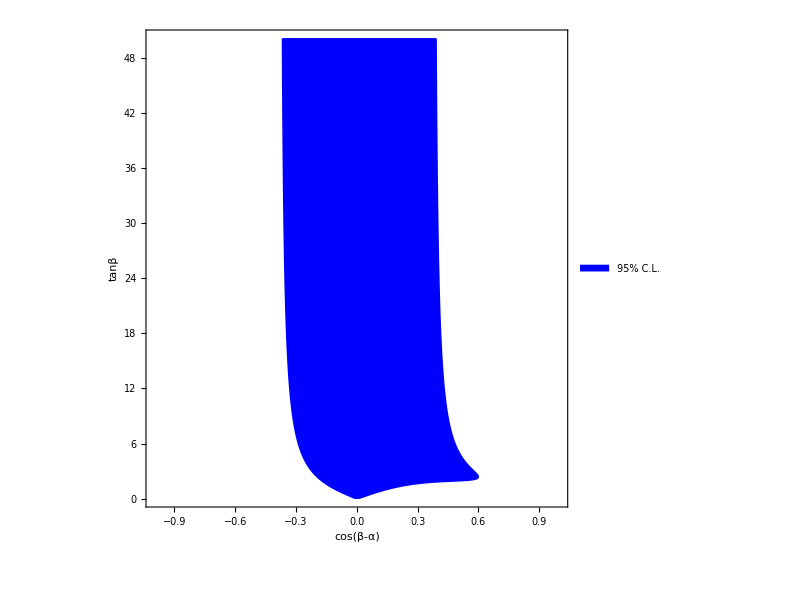

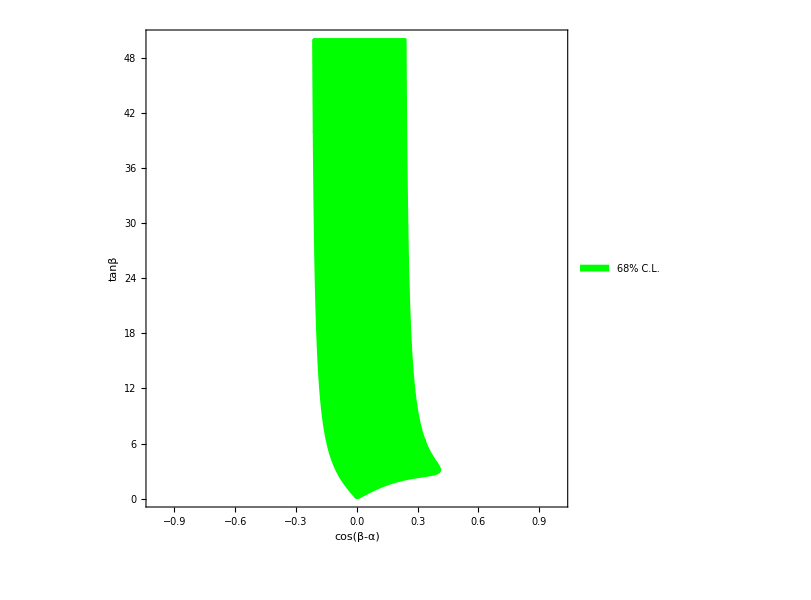

```mathematica
ChiSq95=Chi2Rx95[ghtt[-ArcCos[Cab]+ArcTan[tb],tb],ghbb[-ArcCos[Cab]+ArcTan[tb],tb],ghtautau[-ArcCos[Cab]+ArcTan[tb],tb],ghZZ[Sqrt[1-Cab^2]],ghWW[Sqrt[1-Cab^2]],0,2000]
ChiSq68=Chi2Rx68[ghtt[-ArcCos[Cab]+ArcTan[tb],tb],ghbb[-ArcCos[Cab]+ArcTan[tb],tb],ghtautau[-ArcCos[Cab]+ArcTan[tb],tb],ghZZ[Sqrt[1-Cab^2]],ghWW[Sqrt[1-Cab^2]],0,2000]
```

```mathematica
(***********************************************************************************
***********************************************************************************
***********************************************************************************)
```

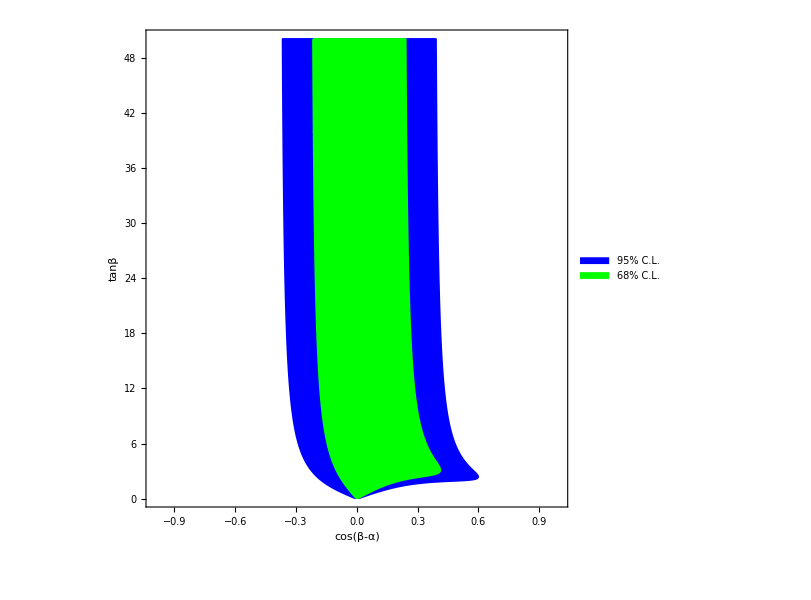

```mathematica
ChiSquareRx=Show[ChiSq95,ChiSq68]
```